```mathematica
Remove["Global`*"]
```

```mathematica
coinTossValues = {p->1/2, q-> 1/2, z1 -> 3/2, z2-> 3/5, k->1};
```

## Fractional compounding

```mathematica
f[x_, M_, z1_, z2_, p_, q_] := x Log[x] + (1-x) Log[1-x] - x Log[p] - (1-x) Log[q] + (1/(2 M))Log[2 π M x (1-x)];
g0[x_, M_, z1_, z2_, k_] := -k x Log[z1] - k(1-x) Log[z2];
g1[x_, M_, z1_, z2_, k_, η_] := -(1/M)(1/(1-η))Log[ (1+M(x(z1^(k(1-η))-1)+(1-x)(z2^(k(1-η))-1)))];
h0[x_, M_, z1_, z2_, p_, q_, k_] := f[x, M, z1, z2, p, q] + g0[x, M, z1, z2, k] ;
h1[x_, M_, z1_, z2_, p_, q_, k_, η_] := f[x, M, z1, z2, p, q] + g1[x, M, z1, z2, k, η]
```

```mathematica
TVal=100;
Manipulate[
p1 = Plot[f[x, TVal, z1, z2, p, q] /. coinTossValues, {x, 0, 1}, PlotStyle->{Red}, PlotLegends->{"f(x,T)"}, PlotRange->{{0,1},{-0.25,1}}];
p2 =  Plot[ g1[x, TVal, z1, z2, 1, η]  /. coinTossValues, {x, 0, 1},  PlotStyle->{Blue}, PlotLegends->{"g(x, T, η, k"},PlotRange->{{0,1},{-0.25,1}} ];
Show[{p1,p2}, AspectRatio->1], {η, 0, 1}]
```

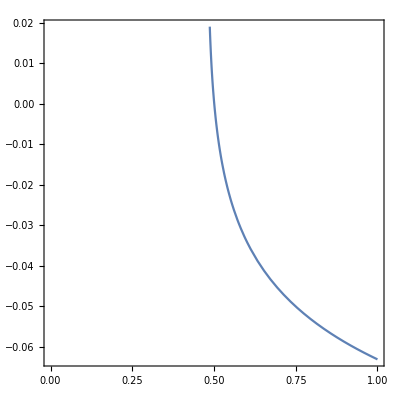

```mathematica
Plot[ g1[x, TVal, z1, z2, 1, 1/2]  /. coinTossValues, {x, 0, 1}]
```

Strategy:
- Verify that Lim_{η->} g1[x, η] = g0[x]
- Verify that Lim_{η->} g1’[x, η] = g0’[x]
- Find solution of g0’[x] = 0 as T-> \infty, x*0
- Find solution of g1’[x, η] =0 as T-> \infty, x*1[η]
- Verify that Lim_{η->0} x*1[η] = x*[0]

```mathematica
A = z1 >0 && z2 >0 && x>0 && x<1 && T>1 && k>=1 && p>0 && p<1 && q>0 && q<1;
chk1 = Limit[g1[x, T, z1, z2, k, η], η->1, Assumptions->A  ]
chk1 = FullSimplify[chk1, Assumptions->A]
```

-k (x Log[z1]+Log[z2]-x Log[z2])

-k x Log[z1]+k (-1+x) Log[z2]

```mathematica
chk1 - g0[x, T, z1, z2, k] // FullSimplify
```

0

```mathematica
T1 = D[g0[x, T, z1, z2, k], x];
T2 = D[g1[x, T, z1, z2, k, η], x];
FullSimplify[T1, Assumptions->A]
FullSimplify[T2, Assumptions->A]
chk2 = Limit[T2, η->1, Assumptions->A  ]
FullSimplify[chk2 - T1 , Assumptions->A]
```

k Log[z2/z1]

(z1^(k-k η)-z2^(k-k η))/((1+T (-1+z2^(k-k η)+x (z1^(k-k η)-z2^(k-k η)))) (-1+η))

k Log[z2/z1]

0

#### Find critical points of the exponents

```mathematica
T1 = D[f[x, T, z1, z2, p, q] + g0[x, T, z1, z2, k], x];
T2 = D[f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η], x];
FullSimplify[T1, Assumptions->A]
FullSimplify[T2, Assumptions->A]
```

(1-2 x)/(2 T x-2 T x^2)+Log[(q x)/(p-p x)]+k Log[z2/z1]

1/(2 T x)-1/(2 T-2 T x)+(z1^(k-k η)-z2^(k-k η))/((1+T (-1+z2^(k-k η)+x (z1^(k-k η)-z2^(k-k η)))) (-1+η))+Log[(q x)/(p-p x)]

```mathematica
U1 = Normal[Series[Expand[T1 /. T-> 1/ϵ /. x-> x0 + ϵ x1], {ϵ, 0, 1}]];
U11 = Coefficient[U1, ϵ]
U10 = U1 - ϵ U11
xStar0 =  (x0 /. Solve[U10 ==0, x0])[[1]]
```

(-1+2 x0-2 x1)/(2 (-1+x0) x0)

-Log[p]+Log[q]-Log[1-x0]+Log[x0]-k Log[z1]+k Log[z2]

(p z1^k)/(p z1^k+q z2^k)

```mathematica
U2 = Normal[Series[Expand[T2 /. T-> 1/ϵ /. x-> x0 + ϵ x1], {ϵ, 0, 1}]]
U21 = Coefficient[U2, ϵ]
U20 = U2 - ϵ U21
xStar1 = (x0 /. Solve[U20 ==0, x0] )[[1]]
```

ϵ (1/(-1+x0)-1/(2 (-1+x0) x0)-x1/(-1+x0)+x1/x0-z1^(k (1-η))/((x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η)))) (1-η))+z2^(k (1-η))/((x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η)))) (1-η)))-Log[p]+Log[q]-Log[1-x0]+Log[x0]

1/(-1+x0)-1/(2 (-1+x0) x0)-x1/(-1+x0)+x1/x0-z1^(k (1-η))/((x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η)))) (1-η))+z2^(k (1-η))/((x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η)))) (1-η))

-Log[p]+Log[q]-Log[1-x0]+Log[x0]

p/(p+q)

#### Calculate the expansion of the exponent about the critical point

```mathematica
V1 = Normal[Series[h0[x, T, z1, z2, p, q, k], {x, x0, 2}] ] /. x-> x0 + ζ
V2 = Normal[Series[h1[x, T, z1, z2, p, q, k, η], {x, x0, 2}] ] /. x-> x0 + ζ
```

((-1+2 x0+2 T x0-2 x0^2-2 T x0^2) ζ^2)/(4 T (-1+x0)^2 x0^2)-x0 Log[p]+(-1+x0) Log[q]-(-1+x0) Log[1-x0]+x0 Log[x0]+Log[-2 π T (-1+x0) x0]/(2 T)-k x0 Log[z1]+k (-1+x0) Log[z2]+ζ ((-1+2 x0)/(2 T (-1+x0) x0)-Log[p]+Log[q]-Log[1-x0]+Log[x0]-k Log[z1]+k Log[z2])

ζ^2 (-1/(2 (-1+x0))+1/(2 x0)+(-1+2 x0-2 x0^2)/(4 T (-1+x0)^2 x0^2)-(T (z1^(k (1-η))-z2^(k (1-η)))^2)/(2 (1-T+T x0 z1^(k (1-η))+T z2^(k (1-η))-T x0 z2^(k (1-η)))^2 (-1+η)))-x0 Log[p]+(-1+x0) Log[q]-(-1+x0) Log[1-x0]+x0 Log[x0]+ζ ((-1+2 x0)/(2 T (-1+x0) x0)+(z1^(k (1-η))-z2^(k (1-η)))/((1-T+T x0 z1^(k (1-η))+T z2^(k (1-η))-T x0 z2^(k (1-η))) (-1+η))-Log[p]+Log[q]-Log[1-x0]+Log[x0])+Log[-2 π T (-1+x0) x0]/(2 T)+Log[1+T (x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η))))]/(T (-1+η))

```mathematica
V12 = Coefficient[V1, ζ^2]
V11 = Coefficient[V1 - V12 ζ^2, ζ]
V10 = V1 - V12 ζ^2 - V11 ζ
```

(-1+2 x0+2 T x0-2 x0^2-2 T x0^2)/(4 T (-1+x0)^2 x0^2)

(-1+2 x0)/(2 T (-1+x0) x0)-Log[p]+Log[q]-Log[1-x0]+Log[x0]-k Log[z1]+k Log[z2]

-x0 Log[p]+(-1+x0) Log[q]-(-1+x0) Log[1-x0]+x0 Log[x0]+Log[-2 π T (-1+x0) x0]/(2 T)-k x0 Log[z1]+k (-1+x0) Log[z2]

```mathematica
V22 = Coefficient[V2, ζ^2]
V21 = Coefficient[V2 - V22 ζ^2, ζ]
V20 = V2 - V22 ζ^2 - V21 ζ
```

-1/(2 (-1+x0))+1/(2 x0)+(-1+2 x0-2 x0^2)/(4 T (-1+x0)^2 x0^2)-(T (z1^(k (1-η))-z2^(k (1-η)))^2)/(2 (1-T+T x0 z1^(k (1-η))+T z2^(k (1-η))-T x0 z2^(k (1-η)))^2 (-1+η))

(-1+2 x0)/(2 T (-1+x0) x0)+(z1^(k (1-η))-z2^(k (1-η)))/((1-T+T x0 z1^(k (1-η))+T z2^(k (1-η))-T x0 z2^(k (1-η))) (-1+η))-Log[p]+Log[q]-Log[1-x0]+Log[x0]

-x0 Log[p]+(-1+x0) Log[q]-(-1+x0) Log[1-x0]+x0 Log[x0]+Log[-2 π T (-1+x0) x0]/(2 T)+Log[1+T (x0 (-1+z1^(k (1-η)))-(-1+x0) (-1+z2^(k (1-η))))]/(T (-1+η))

### Check that the first order terms indeed vanish at the critical points of the exponent as T goes to infinity

```mathematica
FullSimplify[V11 /. x0 -> xStar0 /. q-> 1-p, Assumptions->A] /. T-> 1/ϵ /. ϵ->0
```

0

```mathematica
Limit[FullSimplify[V21 /. x0 -> xStar1 /. q-> 1-p, Assumptions->A] /. T-> 1/ϵ, ϵ->0]
```

0

### Calculate values of exponent at the critical point

```mathematica
FullSimplify[-T V10 /. x0 -> xStar0 , Assumptions->A] /. T->1/ϵ
```

Log[p z1^k+q z2^k]/ϵ-1/2 Log[(2 p π q (z1 z2)^k)/((p z1^k+q z2^k)^2 ϵ)]

```mathematica
Series[FullSimplify[-T V20 /. x0 -> xStar1 , Assumptions->A] /. T->1/ϵ, {ϵ, 0, 1}] /. p+q ->1
```

(Log[(2 p π q)/ϵ]-η Log[(2 p π q)/ϵ]-2 Log[(p (-1+z1^(k-k η))+q (-1+z2^(k-k η)))/ϵ])/(2 (-1+η))+(z1^(k η) z2^(k η) ϵ)/((-q z1^(k η) z2^k-p z1^k z2^(k η)+p z1^(k η) z2^(k η)+q z1^(k η) z2^(k η)) (-1+η))+O[ϵ]^2

### Calculate amplitudes at the critical point

```mathematica
T21 = D[f[x, T, z1, z2, p, q] + g0[x, T, z1, z2, k], {x, 2}]
T22 = D[f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η], {x,2}]
```

1/(1-x)+1/x+(-2/((1-x) x)-(2 π T (1-x)-2 π T x)/(2 π T (1-x) x^2)+(2 π T (1-x)-2 π T x)/(2 π T (1-x)^2 x))/(2 T)

1/(1-x)+1/x+(-2/((1-x) x)-(2 π T (1-x)-2 π T x)/(2 π T (1-x) x^2)+(2 π T (1-x)-2 π T x)/(2 π T (1-x)^2 x))/(2 T)+(T (z1^(k (1-η))-z2^(k (1-η)))^2)/((1+T (x (-1+z1^(k (1-η)))+(1-x) (-1+z2^(k (1-η)))))^2 (1-η))

```mathematica
A1 = FullSimplify[T21 /. x-> xStar0, Assumptions->A]
```

-((z1 z2)^(-2 k) (p z1^k+q z2^k)^2 (p^2 z1^(2 k)+q^2 z2^(2 k)-2 p q T (z1 z2)^k))/(2 p^2 q^2 T)

```mathematica
Series[A1/. T-> 1/ϵ, {ϵ, 0, 2}]
```

((z1 z2)^-k (p z1^k+q z2^k)^2)/(p q)-(((z1 z2)^(-2 k) (p z1^k+q z2^k)^2 (p^2 z1^(2 k)+q^2 z2^(2 k))) ϵ)/(2 (p^2 q^2))+O[ϵ]^3

```mathematica
A2 = FullSimplify[T22 /. x-> xStar1, Assumptions->A]
```

1/2 (p+q) (2/p+2/q+(1-p^2/q^2)/(p T)-(2 (p+q))/(p q T)+(1-q^2/p^2)/(q T)-(2 (p+q) T (z1^(k-k η)-z2^(k-k η))^2)/((p+q+p T (-1+z1^(k-k η))+q T (-1+z2^(k-k η)))^2 (-1+η)))

```mathematica
Series[A2 /. T-> 1/ϵ, {ϵ, 0, 2}]
```

(p+q)^2/(p q)+1/2 (p+q) ((1-p^2/q^2)/p-(2 (p+q))/(p q)+(1-q^2/p^2)/q-(2 (p+q) (z1^(k-k η)-z2^(k-k η))^2)/((p (-1+z1^(k-k η))+q (-1+z2^(k-k η)))^2 (-1+η))) ϵ+(2 (p+q)^3 (z1^(k-k η)-z2^(k-k η))^2 ϵ^2)/((p (-1+z1^(k-k η))+q (-1+z2^(k-k η)))^3 (-1+η))+O[ϵ]^3

```mathematica
hope = ((p(z1^(k(1-η))-1) + q(z2^(k(1-η))-1))T)^(1/(1-η))
```

(T (p (-1+z1^(k (1-η)))+q (-1+z2^(k (1-η)))))^(1/(1-η))

```mathematica
hope /. {η->1/2,k->1, p->1/2, q->1/2, z1-> (g+r), z2->g-r} // FullSimplify
```

1/4 (-2+√(g-r)+√(g+r))^2 T^2

```mathematica
ampl = FullSimplify[hope /. {T->1, η ->1-ϵ ,k->1, p->1/2, q->1/2, z1-> (g+r), z2->g-r}  /. {g->1, r->1/4}, Assumptions->ϵ>0]
```

2^(-1/ϵ) (-2+(3/4)^ϵ+(5/4)^ϵ)^(1/ϵ)

```mathematica
coinTossValues = {p->1/2, q-> 1/2, z1 -> 3/2, z2-> 3/5, k->1};
TVal=100;
Manipulate[
p1 = Plot[f[x, TVal, z1, z2, p, q] + g0[x, TVal, z1, z2, 1] /. coinTossValues, {x, 0, 1}, PlotStyle->{Red}, PlotLegends->{"Multiplicative"}];
p2 =  Plot[f[x, TVal, z1, z2, p, q] + g1[x, TVal, z1, z2, 1, η]  /. coinTossValues, {x, 0, 1},  PlotStyle->{Blue}, PlotLegends->{"η compounding"}];
Show[{p1,p2}, AspectRatio->1], {η, 0, 1}]
```

#### Try to calculate next order correction (in T) to the root since the leading order is a poor approximation of the position of the root at η=1

```mathematica
U2 = Normal[Series[Expand[T2 /. T-> 1/ϵ ], {ϵ, 0, 1}]]
U2 = Normal[Series[Expand[T2 /. T-> 1/ϵ/. x-> x0 + ϵ x1 ], {ϵ, 0, 1}]]
U21 = Coefficient[U2, ϵ];
U20 = U2 - ϵ U21;
```

-1/(10 (1-x))+1/(20 (1-x) x)-(2. (1. z1^(0.5 k)-1. z2^(0.5 k)) ϵ)/(-1.+x z1^(0.5 k)+z2^(0.5 k)-1. x z2^(0.5 k))-Log[p]+Log[q]-Log[1-x]+Log[x]

1/(10 (-1+x0))-1/(20 (-1+x0) x0)+(-x1/(-1+x0)+x1/x0+x1/(10 (-1+x0) x0)+((-1+2 x0) x1)/(20 (-1+x0)^2 x0^2)-((-1+2 x0) x1)/(10 (-1+x0)^2 x0)-(2. z1^(0.5 k))/(x0 (-1+z1^(0.5 k))-(-1+x0) (-1+z2^(0.5 k)))+(2. z2^(0.5 k))/(x0 (-1+z1^(0.5 k))-(-1+x0) (-1+z2^(0.5 k)))) ϵ-Log[p]+Log[q]-Log[1-x0]+Log[x0]

```mathematica
U21 = Coefficient[U2, ϵ];
U20 = U2 - ϵ U21;
```

#### Zeroth order

```mathematica
U20
xStar10 = (x0 /. Solve[U20 ==0, x0] )[[1]]
```

1/(10 (-1+x0))-1/(20 (-1+x0) x0)-Log[p]+Log[q]-Log[1-x0]+Log[x0]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1/(10 (-1+x0))-1/(20 (-1+x0) x0)-Log[p]+Log[q]-Log[1+Times[«2»]]+Log[x0]==0,x0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x0

#### First order

```mathematica
U21
U21 = Expand[FullSimplify[U21 /. x0-> xStar10, Assumptions->A]];
U21x1 = FullSimplify[Coefficient[U21, x1], Assumptions->A]
U21rest = FullSimplify[ U21 - U21x1 x1, Assumptions->A]
```

-x1/(-1+x0)+x1/x0+x1/(10 (-1+x0) x0)+((-1+2 x0) x1)/(20 (-1+x0)^2 x0^2)-((-1+2 x0) x1)/(10 (-1+x0)^2 x0)-(2. z1^(0.5 k))/(x0 (-1+z1^(0.5 k))-(-1+x0) (-1+z2^(0.5 k)))+(2. z2^(0.5 k))/(x0 (-1+z1^(0.5 k))-(-1+x0) (-1+z2^(0.5 k)))

-(1+22 (-1+x0) x0)/(20 (-1+x0)^2 x0^2)

1/(-0.5 x0+(0.5-0.5 z2^(0.5 k))/(1. z1^(0.5 k)-1. z2^(0.5 k)))

```mathematica
xStar11 = (x1 /. Solve[ U21 == 0, x1 ])[[1]]
```

-0.05/((-1.1/(-1.+x0)^2-0.05/((-1.+x0)^2 x0^2)+1.1/((-1.+x0)^2 x0)) (-0.025 x0+(0.025-0.025 z2^(0.5 k))/(1. z1^(0.5 k)-1. z2^(0.5 k))))

```mathematica
xStar11 = FullSimplify[xStar11, Assumptions->A] /. p+q ->1
```

-(1.81818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))

#### Correction to the root diverges as η -> 1:

```mathematica
FullSimplify[Limit[xStar11, η->1], Assumptions->A]
```

Limit::ivar: 0.5 is not a valid variable.

lim_(0.5→1) -(1.81818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))

```mathematica
FullSimplify[xStar11 /. k->1, Assumptions->A]
```

-(1.81818 (-1.+x0)^2 x0^2 (1. z1^0.5-1. z2^0.5))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^0.5+1. z2^0.5-1. x0 z2^0.5))

#### Now try evaluating amplitudes and exponents at the critical point Leading order:

```mathematica
F2 = D[f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η], {x,2}];
F2 = F2 /. x-> xStar10  /. T->1/ϵ;
SeriesCoefficient[Series[F2, {ϵ, 0, 1}],0]
SeriesCoefficient[Series[F2, {ϵ, 0, 1}],1]
```

(-1+22 x0-22 x0^2)/(20 (-1+x0)^2 x0^2)

0

```mathematica
F0 = Exp[-T (f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η])] /. x-> xStar10  /. T->1/ϵ
F0 = FullSimplify[F0 , Assumptions->A]
```

ⅇ^(-10 (-x0 Log[p]-(1-x0) Log[q]+(1-x0) Log[1-x0]+x0 Log[x0]+1/20 Log[20 π (1-x0) x0]-0.2 Log[1+(x0 (-1+z1^(0.5 k))+(1-x0) (-1+z2^(0.5 k)))/ϵ]))

(0.126157 ((1-x0)/q)^(-10.+10. x0) (x0/p)^(-10. x0) ((-1+x0 z1^(0.5 k)-(-1+x0) z2^(0.5 k)+ϵ)/ϵ)^2.)/((x0-x0^2)^0.5)

```mathematica
F0 = FullSimplify[F0 /. (p+q) ->1 /. Assumptions->A]
```

(0.126157 ((1-x0)/q)^(-10.+10. x0) (x0/p)^(-10. x0) ((-1+x0 z1^(0.5 k)-(-1+x0) z2^(0.5 k)+ϵ)/ϵ)^2.)/((x0-x0^2)^0.5)

```mathematica
answer = Asymptotic[√((2 π)/(F2 ϵ))F0, ϵ->0, Assumptions->A && (p+q)==1]
```

(1.41421 p^(10. x0) q^(10.-10. x0) (1-x0)^(-10.+10. x0) x0^(-10. x0) √(-((-1+x0)^2 x0^2)/((1-22 x0+22 x0^2) ϵ)) ((-1+x0 z1^(0.5 k)-(-1+x0) z2^(0.5 k)+ϵ)/ϵ)^2.)/((x0-x0^2)^0.5)

#### First order

```mathematica
F2 = D[f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η], {x,2}];
F2 = F2 /. x-> (xStar10 + (1/T)xStar11)  /. T->1/ϵ;
SeriesCoefficient[Series[F2, {ϵ, 0, 1}],0]
SeriesCoefficient[Series[F2, {ϵ, 0, 1}],1]
```

1/(x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+1/(1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+1/20 (-(2/((x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))))+(-20 π (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+20 π (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))))/(20 π (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^2)-(-20 π (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+20 π (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))))/(20 π (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^2 (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))))

0

```mathematica
F0 = Exp[-T (f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, k, η])] /.x-> (xStar10 + (1/T)xStar11)  /. T->1/ϵ
```

ⅇ^(-10 (-((x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) Log[p])-(1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) Log[q]+(x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) Log[x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))]+(1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) Log[1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))]+1/20 Log[20 π (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))]-0.2 Log[1+((-1+z1^(0.5 k)) (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+(-1+z2^(0.5 k)) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))))/ϵ]))

```mathematica
answer2 = Asymptotic[√((2 π)/(F2 ϵ))F0, ϵ->0, Assumptions->A && (p+q)==1]
```

(1/ϵ((-1+z1^(0.5 k)) (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))+(-1+z2^(0.5 k)) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))))^(0.0909091/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(2. x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(2. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.0909091 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(2. x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(2. x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.0909091 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(2.09091 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(4. x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(2. x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (0.977718 p^((0.454545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1.36364 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(6.36364 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.63636 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(16.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (20 π)^(-0.0227273/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.522727 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1. x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) q^(0.454545/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10.4545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(20. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.63636 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(16.3636 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10.9091 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(28.6364 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(26.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^(-(0.454545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(1.36364 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(6.36364 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.63636 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(16.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^(-0.454545/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10.4545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(20. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.63636 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(16.3636 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10.9091 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(28.6364 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(26.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) ((x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))))^(-0.0227273/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.522727 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1. x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) √(((-0.0555556+1.27778 x0-2.44444 x0^2+1.22222 x0^3+0.0555556 x0 z1^(0.5 k)-1.05556 x0^2 z1^(0.5 k)+2. x0^3 z1^(0.5 k)-1. x0^4 z1^(0.5 k)+0.0555556 z2^(0.5 k)-1.33333 x0 z2^(0.5 k)+3.5 x0^2 z2^(0.5 k)-3.22222 x0^3 z2^(0.5 k)+1. x0^4 z2^(0.5 k))^2 (0.0555556 x0-1.22222 x0^2+1.22222 x0^3+0.166667 x0^2 z1^(0.5 k)+0.777778 x0^3 z1^(0.5 k)-1. x0^4 z1^(0.5 k)-0.0555556 x0 z2^(0.5 k)+1.05556 x0^2 z2^(0.5 k)-2. x0^3 z2^(0.5 k)+1. x0^4 z2^(0.5 k))^2)/((-7.24648×10^-8+7.97113×10^-6 x0-0.000358701 x0^2+0.00841751 x0^3-0.108375 x0^4+0.736111 x0^5-2.38426 x0^6+4.07407 x0^7-3.81944 x0^8+1.86728 x0^9-0.373457 x0^10+2.89859×10^-7 x0 z1^(0.5 k)-0.0000255076 x0^2 z1^(0.5 k)+0.00098842 x0^3 z1^(0.5 k)-0.0222745 x0^4 z1^(0.5 k)+0.306244 x0^5 z1^(0.5 k)-2.33656 x0^6 z1^(0.5 k)+8.03002 x0^7 z1^(0.5 k)-14.1759 x0^8 z1^(0.5 k)+13.5617 x0^9 z1^(0.5 k)-6.72222 x0^10 z1^(0.5 k)+1.35802 x0^11 z1^(0.5 k)-4.34789×10^-7 x0^2 z1^(1. k)+0.0000286961 x0^3 z1^(1. k)-0.000838562 x0^4 z1^(1. k)+0.0175429 x0^5 z1^(1. k)-0.286591 x0^6 z1^(1. k)+2.67841 x0^7 z1^(1. k)-9.98095 x0^8 z1^(1. k)+18.3359 x0^9 z1^(1. k)-17.9548 x0^10 z1^(1. k)+9.03704 x0^11 z1^(1. k)-1.84568 x0^12 z1^(1. k)+2.89859×10^-7 x0^3 z1^(1.5 k)-0.0000127538 x0^4 z1^(1.5 k)+0.000146669 x0^5 z1^(1.5 k)-0.0019322 x0^6 z1^(1.5 k)+0.0879502 x0^7 z1^(1.5 k)-1.29159 x0^8 z1^(1.5 k)+5.40886 x0^9 z1^(1.5 k)-10.4402 x0^10 z1^(1.5 k)+10.5022 x0^11 z1^(1.5 k)-5.37654 x0^12 z1^(1.5 k)+1.11111 x0^13 z1^(1.5 k)-7.24648×10^-8 x0^4 z1^(2. k)+1.59423×10^-6 x0^5 z1^(2. k)+0.0000621748 x0^6 z1^(2. k)-0.00175365 x0^7 z1^(2. k)+0.000771605 x0^8 z1^(2. k)+0.213626 x0^9 z1^(2. k)-1.07368 x0^10 z1^(2. k)+2.20623 x0^11 z1^(2. k)-2.2897 x0^12 z1^(2. k)+1.19444 x0^13 z1^(2. k)-0.25 x0^14 z1^(2. k)+2.89859×10^-7 z2^(0.5 k)-0.0000321744 x0 z2^(0.5 k)+0.00146031 x0^2 z2^(0.5 k)-0.0346585 x0^3 z2^(0.5 k)+0.455776 x0^4 z2^(0.5 k)-3.25069 x0^5 z2^(0.5 k)+11.8736 x0^6 z2^(0.5 k)-24.3263 x0^7 z2^(0.5 k)+29.4537 x0^8 z2^(0.5 k)-21.0309 x0^9 z2^(0.5 k)+8.21605 x0^10 z2^(0.5 k)-1.35802 x0^11 z2^(0.5 k)+8.69577×10^-7 x0^2 z1^(1. k) z2^(0.5 k)-0.0000582617 x0^3 z1^(1. k) z2^(0.5 k)+0.00171539 x0^4 z1^(1. k) z2^(0.5 k)-0.0355257 x0^5 z1^(1. k) z2^(0.5 k)+0.578978 x0^6 z1^(1. k) z2^(0.5 k)-5.62068 x0^7 z1^(1. k) z2^(0.5 k)+23.8367 x0^8 z1^(1. k) z2^(0.5 k)-52.8983 x0^9 z1^(1. k) z2^(0.5 k)+67.2304 x0^10 z1^(1. k) z2^(0.5 k)-49.5808 x0^11 z1^(1. k) z2^(0.5 k)+19.821 x0^12 z1^(1. k) z2^(0.5 k)-3.33333 x0^13 z1^(1. k) z2^(0.5 k)-2.89859×10^-7 x0^3 z1^(1.5 k) z2^(0.5 k)+0.0000130437 x0^4 z1^(1.5 k) z2^(0.5 k)-0.000153046 x0^5 z1^(1.5 k) z2^(0.5 k)+0.0016835 x0^6 z1^(1.5 k) z2^(0.5 k)-0.0809356 x0^7 z1^(1.5 k) z2^(0.5 k)+1.2885 x0^8 z1^(1.5 k) z2^(0.5 k)-6.26337 x0^9 z1^(1.5 k) z2^(0.5 k)+14.735 x0^10 z1^(1.5 k) z2^(0.5 k)-19.3272 x0^11 z1^(1.5 k) z2^(0.5 k)+14.5354 x0^12 z1^(1.5 k) z2^(0.5 k)-5.88889 x0^13 z1^(1.5 k) z2^(0.5 k)+1. x0^14 z1^(1.5 k) z2^(0.5 k)-4.34789×10^-7 z2^(1. k)+0.0000486963 x0 z2^(1. k)-0.00222916 x0^2 z2^(1. k)+0.053499 x0^3 z2^(1. k)-0.717915 x0^4 z2^(1. k)+5.35294 x0^5 z2^(1. k)-21.6018 x0^6 z2^(1. k)+51.2129 x0^7 z2^(1. k)-75.4254 x0^8 z2^(1. k)+70.2247 x0^9 z2^(1. k)-40.3622 x0^10 z2^(1. k)+13.1111 x0^11 z2^(1. k)-1.84568 x0^12 z2^(1. k)+8.69577×10^-7 x0 z1^(0.5 k) z2^(1. k)-0.000078262 x0^2 z1^(0.5 k) z2^(1. k)+0.00308091 x0^3 z1^(0.5 k) z2^(1. k)-0.070216 x0^4 z1^(0.5 k) z2^(1. k)+0.989344 x0^5 z1^(0.5 k) z2^(1. k)-8.16184 x0^6 z1^(0.5 k) z2^(1. k)+35.0676 x0^7 z1^(0.5 k) z2^(1. k)-86.3263 x0^8 z1^(0.5 k) z2^(1. k)+130.255 x0^9 z1^(0.5 k) z2^(1. k)-123.307 x0^10 z1^(0.5 k) z2^(1. k)+71.729 x0^11 z1^(0.5 k) z2^(1. k)-23.5123 x0^12 z1^(0.5 k) z2^(1. k)+3.33333 x0^13 z1^(0.5 k) z2^(1. k)+2.89859×10^-7 z2^(1.5 k)-0.0000327541 x0 z2^(1.5 k)+0.00151219 x0^2 z2^(1.5 k)-0.036693 x0^3 z2^(1.5 k)+0.502015 x0^4 z2^(1.5 k)-3.89841 x0^5 z2^(1.5 k)+17.1218 x0^6 z2^(1.5 k)-45.8311 x0^7 z2^(1.5 k)+79.059 x0^8 z2^(1.5 k)-90.2349 x0^9 z2^(1.5 k)+68.0104 x0^10 z2^(1.5 k)-32.6504 x0^11 z2^(1.5 k)+9.0679 x0^12 z2^(1.5 k)-1.11111 x0^13 z2^(1.5 k)-2.89859×10^-7 x0 z1^(0.5 k) z2^(1.5 k)+0.0000263772 x0^2 z1^(0.5 k) z2^(1.5 k)-0.00104668 x0^3 z1^(0.5 k) z2^(1.5 k)+0.0239902 x0^4 z1^(0.5 k) z2^(1.5 k)-0.341776 x0^5 z1^(0.5 k) z2^(1.5 k)+2.91529 x0^6 z1^(0.5 k) z2^(1.5 k)-13.6437 x0^7 z1^(0.5 k) z2^(1.5 k)+38.0095 x0^8 z1^(0.5 k) z2^(1.5 k)-67.3145 x0^9 z1^(0.5 k) z2^(1.5 k)+78.2473 x0^10 z1^(0.5 k) z2^(1.5 k)-59.7637 x0^11 z1^(0.5 k) z2^(1.5 k)+28.9798 x0^12 z1^(0.5 k) z2^(1.5 k)-8.11111 x0^13 z1^(0.5 k) z2^(1.5 k)+1. x0^14 z1^(0.5 k) z2^(1.5 k)-7.24648×10^-8 z2^(2. k)+8.26098×10^-6 x0 z2^(2. k)-0.000384643 x0^2 z2^(2. k)+0.00943491 x0^3 z2^(2. k)-0.131501 x0^4 z2^(2. k)+1.06005 x0^5 z2^(2. k)-5.00928 x0^6 z2^(2. k)+14.8687 x0^7 z2^(2. k)-29.2671 x0^8 z2^(2. k)+39.3874 x0^9 z2^(2. k)-36.5644 x0^10 z2^(2. k)+23.1035 x0^11 z2^(2. k)-9.51192 x0^12 z2^(2. k)+2.30556 x0^13 z2^(2. k)-0.25 x0^14 z2^(2. k)-8.69577×10^-7 x0 (z1 z2)^(0.5 k)+0.0000773924 x0^2 (z1 z2)^(0.5 k)-0.00302265 x0^3 (z1 z2)^(0.5 k)+0.0685007 x0^4 (z1 z2)^(0.5 k)-0.953818 x0^5 (z1 z2)^(0.5 k)+7.58286 x0^6 (z1 z2)^(0.5 k)-29.4469 x0^7 (z1 z2)^(0.5 k)+62.4897 x0^8 (z1 z2)^(0.5 k)-77.3569 x0^9 (z1 z2)^(0.5 k)+56.0763 x0^10 (z1 z2)^(0.5 k)-22.1481 x0^11 (z1 z2)^(0.5 k)+3.69136 x0^12 (z1 z2)^(0.5 k)-4.34789×10^-7 x0^2 (z1 z2)^(1. k)+0.0000295656 x0^3 (z1 z2)^(1. k)-0.000877259 x0^4 (z1 z2)^(1. k)+0.0179924 x0^5 (z1 z2)^(1. k)-0.292014 x0^6 (z1 z2)^(1. k)+2.93174 x0^7 (z1 z2)^(1. k)-13.8511 x0^8 (z1 z2)^(1. k)+35.8442 x0^9 (z1 z2)^(1. k)-55.7176 x0^10 (z1 z2)^(1. k)+53.7811 x0^11 (z1 z2)^(1. k)-31.7135 x0^12 (z1 z2)^(1. k)+10.5 x0^13 (z1 z2)^(1. k)-1.5 x0^14 (z1 z2)^(1. k)) ϵ))-(0.977718 p^((0.454545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1.36364 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(6.36364 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.63636 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(16.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (20 π)^(-0.0227273/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.522727 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1. x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) q^(0.454545/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10.4545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(20. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.63636 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(16.3636 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.454545 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10.9091 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(28.6364 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(26.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (0.0454545-1. x0+1. x0^2-0.0454545 x0 z1^(0.5 k)+1. x0^2 z1^(0.5 k)-1. x0^3 z1^(0.5 k)-0.0454545 z2^(0.5 k)+1.04545 x0 z2^(0.5 k)-2. x0^2 z2^(0.5 k)+1. x0^3 z2^(0.5 k)) (x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^(-(0.454545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(1.36364 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(6.36364 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.63636 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(16.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k))))^(-0.454545/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10.4545 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(20. x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(10. x0^3)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.63636 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(16.3636 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(8.18182 x0^4 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.454545 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(10.9091 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(28.6364 x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(26.3636 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(8.18182 x0^4 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) ((x0-(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))) (1-x0+(0.181818 (-1.+x0)^2 x0^2 (1. z1^(0.5 k)-1. z2^(0.5 k)))/((0.0454545+x0 (-1.+1. x0)) (-1.+1. x0 z1^(0.5 k)+1. z2^(0.5 k)-1. x0 z2^(0.5 k)))))^(-0.0227273/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2)/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 x0 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^2 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.5 x0^3 z1^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(0.0227273 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.522727 x0 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))+(1. x0^2 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))-(0.5 x0^3 z2^(0.5 k))/((0.0454545-1. x0+1. x0^2) (1.-1. x0 z1^(0.5 k)-1. z2^(0.5 k)+1. x0 z2^(0.5 k)))) √(((-0.0555556+1.27778 x0-2.44444 x0^2+1.22222 x0^3+0.0555556 x0 z1^(0.5 k)-1.05556 x0^2 z1^(0.5 k)+2. x0^3 z1^(0.5 k)-1. x0^4 z1^(0.5 k)+0.0555556 z2^(0.5 k)-1.33333 x0 z2^(0.5 k)+3.5 x0^2 z2^(0.5 k)-3.22222 x0^3 z2^(0.5 k)+1. x0^4 z2^(0.5 k))^2 (0.0555556 x0-1.22222 x0^2+1.22222 x0^3+0.166667 x0^2 z1^(0.5 k)+0.777778 x0^3 z1^(0.5 k)-1. x0^4 z1^(0.5 k)-0.0555556 x0 z2^(0.5 k)+1.05556 x0^2 z2^(0.5 k)-2. x0^3 z2^(0.5 k)+1. x0^4 z2^(0.5 k))^2)/((-7.24648×10^-8+7.97113×10^-6 x0-0.000358701 x0^2+0.00841751 x0^3-0.108375 x0^4+0.736111 x0^5-2.38426 x0^6+4.07407 x0^7-3.81944 x0^8+1.86728 x0^9-0.373457 x0^10+2.89859×10^-7 x0 z1^(0.5 k)-0.0000255076 x0^2 z1^(0.5 k)+0.00098842 x0^3 z1^(0.5 k)-0.0222745 x0^4 z1^(0.5 k)+0.306244 x0^5 z1^(0.5 k)-2.33656 x0^6 z1^(0.5 k)+8.03002 x0^7 z1^(0.5 k)-14.1759 x0^8 z1^(0.5 k)+13.5617 x0^9 z1^(0.5 k)-6.72222 x0^10 z1^(0.5 k)+1.35802 x0^11 z1^(0.5 k)-4.34789×10^-7 x0^2 z1^(1. k)+0.0000286961 x0^3 z1^(1. k)-0.000838562 x0^4 z1^(1. k)+0.0175429 x0^5 z1^(1. k)-0.286591 x0^6 z1^(1. k)+2.67841 x0^7 z1^(1. k)-9.98095 x0^8 z1^(1. k)+18.3359 x0^9 z1^(1. k)-17.9548 x0^10 z1^(1. k)+9.03704 x0^11 z1^(1. k)-1.84568 x0^12 z1^(1. k)+2.89859×10^-7 x0^3 z1^(1.5 k)-0.0000127538 x0^4 z1^(1.5 k)+0.000146669 x0^5 z1^(1.5 k)-0.0019322 x0^6 z1^(1.5 k)+0.0879502 x0^7 z1^(1.5 k)-1.29159 x0^8 z1^(1.5 k)+5.40886 x0^9 z1^(1.5 k)-10.4402 x0^10 z1^(1.5 k)+10.5022 x0^11 z1^(1.5 k)-5.37654 x0^12 z1^(1.5 k)+1.11111 x0^13 z1^(1.5 k)-7.24648×10^-8 x0^4 z1^(2. k)+1.59423×10^-6 x0^5 z1^(2. k)+0.0000621748 x0^6 z1^(2. k)-0.00175365 x0^7 z1^(2. k)+0.000771605 x0^8 z1^(2. k)+0.213626 x0^9 z1^(2. k)-1.07368 x0^10 z1^(2. k)+2.20623 x0^11 z1^(2. k)-2.2897 x0^12 z1^(2. k)+1.19444 x0^13 z1^(2. k)-0.25 x0^14 z1^(2. k)+2.89859×10^-7 z2^(0.5 k)-0.0000321744 x0 z2^(0.5 k)+0.00146031 x0^2 z2^(0.5 k)-0.0346585 x0^3 z2^(0.5 k)+0.455776 x0^4 z2^(0.5 k)-3.25069 x0^5 z2^(0.5 k)+11.8736 x0^6 z2^(0.5 k)-24.3263 x0^7 z2^(0.5 k)+29.4537 x0^8 z2^(0.5 k)-21.0309 x0^9 z2^(0.5 k)+8.21605 x0^10 z2^(0.5 k)-1.35802 x0^11 z2^(0.5 k)+8.69577×10^-7 x0^2 z1^(1. k) z2^(0.5 k)-0.0000582617 x0^3 z1^(1. k) z2^(0.5 k)+0.00171539 x0^4 z1^(1. k) z2^(0.5 k)-0.0355257 x0^5 z1^(1. k) z2^(0.5 k)+0.578978 x0^6 z1^(1. k) z2^(0.5 k)-5.62068 x0^7 z1^(1. k) z2^(0.5 k)+23.8367 x0^8 z1^(1. k) z2^(0.5 k)-52.8983 x0^9 z1^(1. k) z2^(0.5 k)+67.2304 x0^10 z1^(1. k) z2^(0.5 k)-49.5808 x0^11 z1^(1. k) z2^(0.5 k)+19.821 x0^12 z1^(1. k) z2^(0.5 k)-3.33333 x0^13 z1^(1. k) z2^(0.5 k)-2.89859×10^-7 x0^3 z1^(1.5 k) z2^(0.5 k)+0.0000130437 x0^4 z1^(1.5 k) z2^(0.5 k)-0.000153046 x0^5 z1^(1.5 k) z2^(0.5 k)+0.0016835 x0^6 z1^(1.5 k) z2^(0.5 k)-0.0809356 x0^7 z1^(1.5 k) z2^(0.5 k)+1.2885 x0^8 z1^(1.5 k) z2^(0.5 k)-6.26337 x0^9 z1^(1.5 k) z2^(0.5 k)+14.735 x0^10 z1^(1.5 k) z2^(0.5 k)-19.3272 x0^11 z1^(1.5 k) z2^(0.5 k)+14.5354 x0^12 z1^(1.5 k) z2^(0.5 k)-5.88889 x0^13 z1^(1.5 k) z2^(0.5 k)+1. x0^14 z1^(1.5 k) z2^(0.5 k)-4.34789×10^-7 z2^(1. k)+0.0000486963 x0 z2^(1. k)-0.00222916 x0^2 z2^(1. k)+0.053499 x0^3 z2^(1. k)-0.717915 x0^4 z2^(1. k)+5.35294 x0^5 z2^(1. k)-21.6018 x0^6 z2^(1. k)+51.2129 x0^7 z2^(1. k)-75.4254 x0^8 z2^(1. k)+70.2247 x0^9 z2^(1. k)-40.3622 x0^10 z2^(1. k)+13.1111 x0^11 z2^(1. k)-1.84568 x0^12 z2^(1. k)+8.69577×10^-7 x0 z1^(0.5 k) z2^(1. k)-0.000078262 x0^2 z1^(0.5 k) z2^(1. k)+0.00308091 x0^3 z1^(0.5 k) z2^(1. k)-0.070216 x0^4 z1^(0.5 k) z2^(1. k)+0.989344 x0^5 z1^(0.5 k) z2^(1. k)-8.16184 x0^6 z1^(0.5 k) z2^(1. k)+35.0676 x0^7 z1^(0.5 k) z2^(1. k)-86.3263 x0^8 z1^(0.5 k) z2^(1. k)+130.255 x0^9 z1^(0.5 k) z2^(1. k)-123.307 x0^10 z1^(0.5 k) z2^(1. k)+71.729 x0^11 z1^(0.5 k) z2^(1. k)-23.5123 x0^12 z1^(0.5 k) z2^(1. k)+3.33333 x0^13 z1^(0.5 k) z2^(1. k)+2.89859×10^-7 z2^(1.5 k)-0.0000327541 x0 z2^(1.5 k)+0.00151219 x0^2 z2^(1.5 k)-0.036693 x0^3 z2^(1.5 k)+0.502015 x0^4 z2^(1.5 k)-3.89841 x0^5 z2^(1.5 k)+17.1218 x0^6 z2^(1.5 k)-45.8311 x0^7 z2^(1.5 k)+79.059 x0^8 z2^(1.5 k)-90.2349 x0^9 z2^(1.5 k)+68.0104 x0^10 z2^(1.5 k)-32.6504 x0^11 z2^(1.5 k)+9.0679 x0^12 z2^(1.5 k)-1.11111 x0^13 z2^(1.5 k)-2.89859×10^-7 x0 z1^(0.5 k) z2^(1.5 k)+0.0000263772 x0^2 z1^(0.5 k) z2^(1.5 k)-0.00104668 x0^3 z1^(0.5 k) z2^(1.5 k)+0.0239902 x0^4 z1^(0.5 k) z2^(1.5 k)-0.341776 x0^5 z1^(0.5 k) z2^(1.5 k)+2.91529 x0^6 z1^(0.5 k) z2^(1.5 k)-13.6437 x0^7 z1^(0.5 k) z2^(1.5 k)+38.0095 x0^8 z1^(0.5 k) z2^(1.5 k)-67.3145 x0^9 z1^(0.5 k) z2^(1.5 k)+78.2473 x0^10 z1^(0.5 k) z2^(1.5 k)-59.7637 x0^11 z1^(0.5 k) z2^(1.5 k)+28.9798 x0^12 z1^(0.5 k) z2^(1.5 k)-8.11111 x0^13 z1^(0.5 k) z2^(1.5 k)+1. x0^14 z1^(0.5 k) z2^(1.5 k)-7.24648×10^-8 z2^(2. k)+8.26098×10^-6 x0 z2^(2. k)-0.000384643 x0^2 z2^(2. k)+0.00943491 x0^3 z2^(2. k)-0.131501 x0^4 z2^(2. k)+1.06005 x0^5 z2^(2. k)-5.00928 x0^6 z2^(2. k)+14.8687 x0^7 z2^(2. k)-29.2671 x0^8 z2^(2. k)+39.3874 x0^9 z2^(2. k)-36.5644 x0^10 z2^(2. k)+23.1035 x0^11 z2^(2. k)-9.51192 x0^12 z2^(2. k)+2.30556 x0^13 z2^(2. k)-0.25 x0^14 z2^(2. k)-8.69577×10^-7 x0 (z1 z2)^(0.5 k)+0.0000773924 x0^2 (z1 z2)^(0.5 k)-0.00302265 x0^3 (z1 z2)^(0.5 k)+0.0685007 x0^4 (z1 z2)^(0.5 k)-0.953818 x0^5 (z1 z2)^(0.5 k)+7.58286 x0^6 (z1 z2)^(0.5 k)-29.4469 x0^7 (z1 z2)^(0.5 k)+62.4897 x0^8 (z1 z2)^(0.5 k)-77.3569 x0^9 (z1 z2)^(0.5 k)+56.0763 x0^10 (z1 z2)^(0.5 k)-22.1481 x0^11 (z1 z2)^(0.5 k)+3.69136 x0^12 (z1 z2)^(0.5 k)-4.34789×10^-7 x0^2 (z1 z2)^(1. k)+0.0000295656 x0^3 (z1 z2)^(1. k)-0.000877259 x0^4 (z1 z2)^(1. k)+0.0179924 x0^5 (z1 z2)^(1. k)-0.292014 x0^6 (z1 z2)^(1. k)+2.93174 x0^7 (z1 z2)^(1. k)-13.8511 x0^8 (z1 z2)^(1. k)+35.8442 x0^9 (z1 z2)^(1. k)-55.7176 x0^10 (z1 z2)^(1. k)+53.7811 x0^11 (z1 z2)^(1. k)-31.7135 x0^12 (z1 z2)^(1. k)+10.5 x0^13 (z1 z2)^(1. k)-1.5 x0^14 (z1 z2)^(1. k)) ϵ)) ϵ)/(0.0227273-0.5 x0+0.5 x0^2-0.0454545 x0 z1^(0.5 k)+1. x0^2 z1^(0.5 k)-1. x0^3 z1^(0.5 k)-0.0681818 x0^2 z1^(1. k)-0.318182 x0^3 z1^(1. k)+0.409091 x0^4 z1^(1. k)-0.0454545 z2^(0.5 k)+1.04545 x0 z2^(0.5 k)-2. x0^2 z2^(0.5 k)+1. x0^3 z2^(0.5 k)+0.0227273 z2^(1. k)-0.545455 x0 z2^(1. k)+1.43182 x0^2 z2^(1. k)-1.31818 x0^3 z2^(1. k)+0.409091 x0^4 z2^(1. k)+0.0454545 x0 (z1 z2)^(0.5 k)-0.863636 x0^2 (z1 z2)^(0.5 k)+1.63636 x0^3 (z1 z2)^(0.5 k)-0.818182 x0^4 (z1 z2)^(0.5 k)))

```mathematica
Limit[(f[x, TVal, z1, z2, p, q] + g1[x, TVal, z1, z2, 1, 1/2])  /. coinTossValues ,  x->1/4] // N
```

0.124913-0.00628319 ⅈ

```mathematica
(f[x, TVal, z1, z2, p, q] + g1[x, TVal, z1, z2, 1, 1/2] )/. coinTossValues
```

(1-x) Log[2]+x Log[2]+(1-x) Log[1-x]+x Log[x]+Log[2000 π (1-x) x]/2000-1/500 Log[1+1000 ((-1+√(3/5)) (1-x)+(-1+√(3/2)) x)]

```mathematica
((1-x) Log[2]+x Log[2]+(1-x) Log[1-x]+x Log[x]) /. x->1/4 // N
```

0.130812

```mathematica
Log[2000 π (1-x) x]/2000 /. x->1/4 // N
```

0.00353583

```mathematica
-1/500 Log[1+1000 ((-1+√(3/5)) (1-x)+(-1+√(3/2)) x)] /. x->1/4 // N
```

-0.00943461-0.00628319 ⅈ

```mathematica
coinTossValues
```

{p→1/2,q→1/2,z1→3/2,z2→3/5,k→1}

```mathematica
f[x, T, z1, z2, p, q] + g1[x, T, z1, z2, 1, η]
```

-x Log[p]-(1-x) Log[q]+(1-x) Log[1-x]+x Log[x]+Log[2 π T (1-x) x]/(2 T)-Log[1+T (x (-1+z1^(1-η))+(1-x) (-1+z2^(1-η)))]/(T (1-η))